## Formulae an

```mathematica
ExplainContractionCounts[g_,e_]:=Block[{
gBis=SortGraph[g], 
taken={e[[1]],e[[2]]},
comp=SortGraph[VertexDelete[VertexDelete[GraphComplement[g],e[[1]]],e[[2]]]],
nonEdges=0,
remainingNonEdges=0,
result},
result=Table[
If[!EdgeQ[gBis,e[[1]]<->v]&&!EdgeQ[gBis,e[[2]]<->v],
nonEdges++
]
,{v,Select[VertexList[gBis],!MemberQ[taken,#]&]}
];
remainingNonEdges=Length[EdgeList[comp]];
{nonEdges,remainingNonEdges}
]
```

```mathematica
MpgChain[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain[contract],{e,ChromaticPolynomial[g,4]/24}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
MpgChain3[g_]:=Block[{contract, result},
If[VertexCount[g]==3,Return[{ChromaticPolynomial[g,4]/24}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
result=Prepend[MpgChain3[contract],ChromaticPolynomial[g,4]/24];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

```mathematica
Monitor[Select[Table[k->With[{l=Differences[Reverse[MpgChain3[ReadGrof[k]]]]},{Min[l],Max[l]}],{k,10}],#[[2]]≠{0,0}&],k]
```

{4→{0,3},6→{0,3},7→{0,3}}

```mathematica
cm=72/2.54;
```

```mathematica
Clear[MpgChain2]
```

```mathematica
MpgChain2[g_,glayout_:"TutteEmbedding",previous_:{}, positions_:Null,size_:{}]:=Block[{contract, result, coord, newPos=positions,newSize=size, layout, thegraph},
If[VertexCount[g]==2,Return[{}]];
Table[
contract=EdgeContract[g,e];
If[MaximalPlanarQ[contract],
If[positions==Null,
layout = Graph[
SortGraph[g],
GraphLayout->glayout,
GraphHighlightStyle->"Thick",
ImageSize->{10 cm,10 cm}, 
VertexCoordinates->Automatic
];
newPos=First[AbsoluteOptions[layout, VertexCoordinates]][[2]];
newSize=First[AbsoluteOptions[layout, ImageSize]][[2]];
];
coord=newPos;(*Table[newPos[[k]],{k,VertexList[g]}];*)
thegraph=Graph[
Range[Length[newPos]],
EdgeList[g],
GraphHighlightStyle->"Thick",
VertexLabels->Map[If[MemberQ[previous,#],#->ToString[previous],#->Placed[Framed[#,Background->White],Center]]&,VertexList[g]],
GraphHighlight->Select[CollectMPGEdges[g],#=!=e&],
VertexLabelStyle->Directive[Darker[Green],Italic,10],
ImageSize->newSize, 
AspectRatio->1,
EdgeStyle->{e->{Thick,Blue,Dashed}}, 
VertexStyle->Map[#->Yellow&,previous], 
VertexSize->Map[#->Large&,previous],
VertexCoordinates->coord
];
result=Prepend[MpgChain2[contract,glayout,{e[[1]],e[[2]]}, newPos,newSize],{e,Labeled[
thegraph,{Column[ExplainContractionCounts[g,e]],Style[ChromaticPolynomial[g,4]/24,Green ],Grid[Transpose[Map[{#,VertexDegree[g,#]}&,Sort[VertexList[g]]]],Frame->All]}],
Table[
NeighborhoodGraph[ thegraph,v,VertexStyle->{v->Yellow},VertexSize->{v->Large},GraphLayout->"TutteEmbedding"],
{v,{e[[1]],e[[2]]}}
]}];
Goto[stop]
]
,{e,EdgeList[g]}
];
Label[stop];
result
]
```

## experiments come

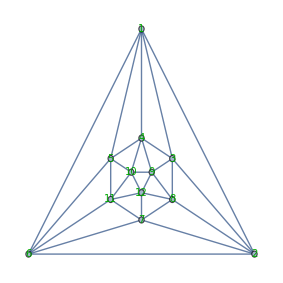
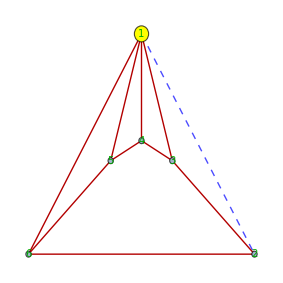
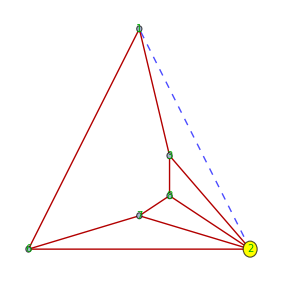
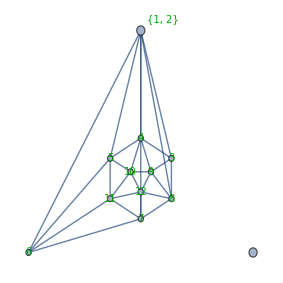
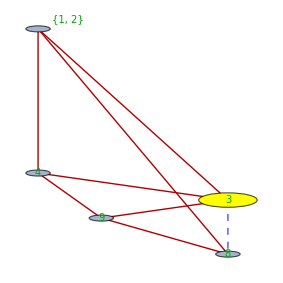
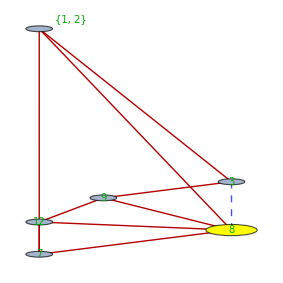
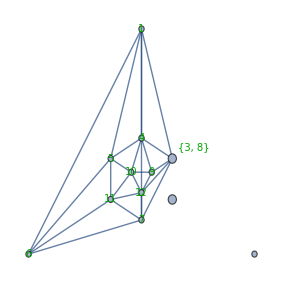
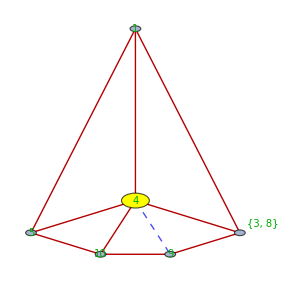
{{1<->2,-Graphics-{4
24,10,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5},{-Graphics-,-Graphics-}},{3<->8,-Graphics-{4
17,8,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
6 | 4 | 5 | 5 | 4 | 5 | 5 | 5 | 5 | 5 | 5},{-Graphics-,-Graphics-}},{4<->9,-Graphics-{3
12,8,1 | 3 | 4 | 5 | 6 | 7 | 9 | 10 | 11 | 12
5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 5},{-Graphics-,-Graphics-}},{5<->10,-Graphics-{2
8,2,1 | 3 | 4 | 5 | 6 | 7 | 10 | 11 | 12
5 | 4 | 5 | 5 | 4 | 5 | 4 | 5 | 5},{-Graphics-,-Graphics-}},{6<->11,-Graphics-{2
4,3,1 | 3 | 4 | 5 | 6 | 7 | 11 | 12
5 | 4 | 4 | 5 | 4 | 5 | 4 | 5},{-Graphics-,-Graphics-}},{7<->12,-Graphics-{0
3,5,1 | 3 | 4 | 5 | 6 | 7 | 12
5 | 4 | 4 | 4 | 4 | 4 | 5},{-Graphics-,-Graphics-}},{3<->1,-Graphics-{0
1,1,1 | 3 | 4 | 5 | 6 | 7
5 | 3 | 4 | 4 | 3 | 5},{-Graphics-,-Graphics-}},{5<->4,-Graphics-{0
0,1,1 | 4 | 5 | 6 | 7
4 | 3 | 4 | 3 | 4},{-Graphics-,-Graphics-}},{7<->6,-Graphics-{0
0,1,1 | 4 | 6 | 7
3 | 3 | 3 | 3},{-Graphics-,-Graphics-}},{4<->1,-Graphics-{0
0,1,1 | 4 | 6
2 | 2 | 2},{-Graphics-,-Graphics-}}}

```mathematica
MpgChain2[Graph[plantri [[1]] ] ]
```

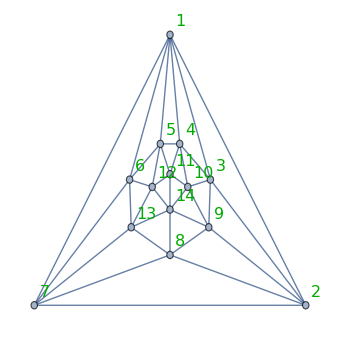
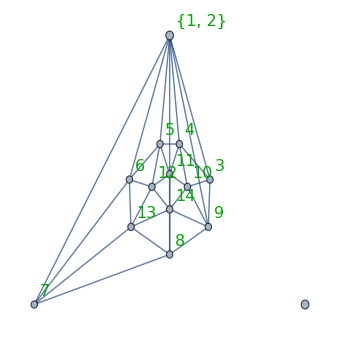
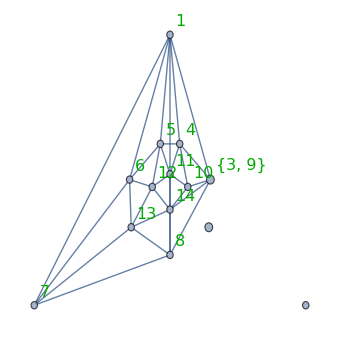
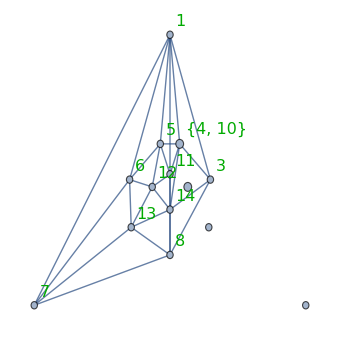
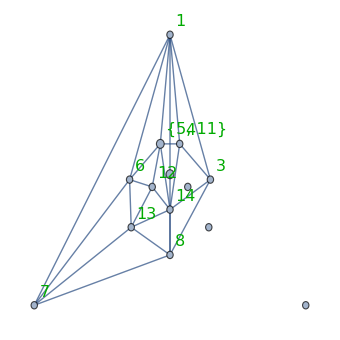
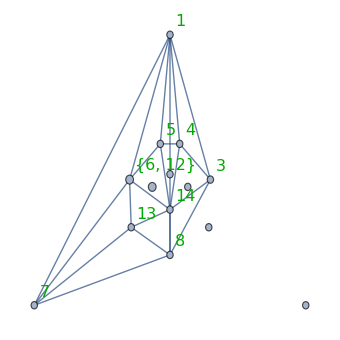
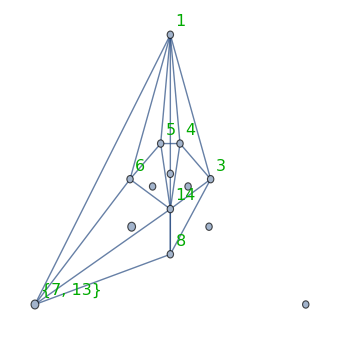
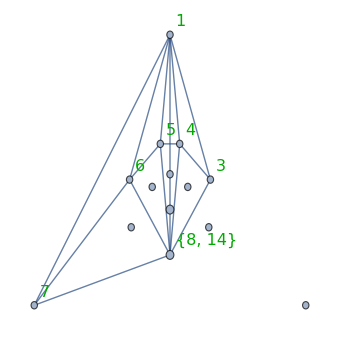
{{1<->2,-Graphics-{5
40,20,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
6 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 6}},{3<->9,-Graphics-{6
30,14,1 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
7 | 4 | 5 | 5 | 5 | 4 | 5 | 5 | 5 | 5 | 5 | 5 | 6}},{4<->10,-Graphics-{5
23,5,1 | 3 | 4 | 5 | 6 | 7 | 8 | 10 | 11 | 12 | 13 | 14
6 | 5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 5 | 6}},{5<->11,-Graphics-{4
17,7,1 | 3 | 4 | 5 | 6 | 7 | 8 | 11 | 12 | 13 | 14
6 | 4 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 5 | 6}},{6<->12,-Graphics-{3
12,5,1 | 3 | 4 | 5 | 6 | 7 | 8 | 12 | 13 | 14
6 | 4 | 4 | 5 | 5 | 4 | 5 | 4 | 5 | 6}},{7<->13,-Graphics-{3
7,9,1 | 3 | 4 | 5 | 6 | 7 | 8 | 13 | 14
6 | 4 | 4 | 4 | 5 | 4 | 5 | 4 | 6}},{8<->14,-Graphics-{0
6,12,1 | 3 | 4 | 5 | 6 | 7 | 8 | 14
6 | 4 | 4 | 4 | 4 | 4 | 4 | 6}},{3<->1,-Graphics-{0
3,1,1 | 3 | 4 | 5 | 6 | 7 | 8
6 | 3 | 4 | 4 | 4 | 3 | 6}},{5<->4,-Graphics-{1
0,1,1 | 4 | 5 | 6 | 7 | 8
5 | 3 | 4 | 4 | 3 | 5}},{7<->6,-Graphics-{0
0,1,1 | 4 | 6 | 7 | 8
4 | 3 | 4 | 3 | 4}},{1<->8,-Graphics-{0
0,1,1 | 4 | 6 | 8
3 | 3 | 3 | 3}},{6<->4,-Graphics-{0
0,1,1 | 4 | 6
2 | 2 | 2}}}

```mathematica
MpgChain2[Graph[plantri [[2]] ] ]
```